# L = 1

```mathematica
l=1;
```

## Setup

This function takes a value of lambda and returns the 100 eigenvalues of the hamiltonian which have the lowest absolute value. nn is the matrix size, dρ is the step size, and ρinf is numerical infinity for the problem.

Because the results of the calculation are highly sensitive to changes in ρinf, I standardized on

```mathematica
RoughCritical[λ_]:=Module[{H,res,dρ,ρinf,nn},
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
(*Print["dρ = "<>ToString[dρ]<>", ρinf = "<>ToString[ρinf]<>", and nn = "<>ToString[nn]<>"."];*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l*(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-100]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam,lnegs,mnegs,hnegs},
mid=l0+(lf-l0)/2;
lnegs=CountNegs[val];
vam=RoughCritical[mid];
mnegs=CountNegs[vam];
hnegs=CountNegs[vaf]
If[lf-l0>range,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]&& mnegs>0),
FindLs[l0,mid,val,vam,range];
];
If[mnegs<hnegs || (hnegs==mnegs && vam[[1]] < vaf[[1]]&&hnegs>0),
FindLs[mid,lf,vam,vaf,range];
];,
res=Append[res,{l0,lf}];
Print["Found one!"];
]
]
```

## Finding candidate ranges

### fix meeee

```mathematica
RangeChunk[low_,high_]:=Module[{res,val,vaf},
res={};
val=RoughCritical[low];
vaf=RoughCritical[high];
FindLs[low,high,val,vaf,1]
]
```

```mathematica
BinaryTest[l0_,lf_]:=Module[{mid,res},
res={};
mid=l0+(lf-l0)/2;
If[lf-l0>range,
res=Append[res,BinaryTest[l0,mid]];
res=Append[res,BinaryTest[mid,lf]];
,
Return[mid];
];
Return[res]
]
```

```mathematica
BinaryTest[1,4]
```

{}

## Rootfinding for Lcs

### Setup

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
(*Print["dρ = "<>ToString[dρ]<>", ρinf = "<>ToString[ρinf]<>", and nn = "<>ToString[nn]<>"."];*)
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(2(*=l(l+1)*))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],eps]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
ListRandomize[list_]:=Module[{order,res},
order=Table[{RandomReal[],i},{i,1,Length[list]}];
order = Sort[order];
res=Table[list[[order[[i,2]]]],{i,1,Length[list]}];
Return[res]
]
```

```mathematica
rhoinfs={40,80};
```

### First calculations: refinement

```mathematica
inputslow=Table[{i,rhoinfs[[1]]*ranges[[i,1]],ranges[[i,1]]-2,ranges[[i,2]]+2},{i,1,Length[ranges]}];
```

```mathematica
inputslow=ListRandomize[inputslow];
```

```mathematica
DistributeDefinitions[Critical,Bisect,CountNegs,Findlc,inputslow]
```

```mathematica
refinement=ParallelTable[Findlc[inputslow[[i]],i,0.25],{i,1,Length[inputslow]}]
```

```mathematica
refinement=Sort[refinement];
```

```mathematica
inputshigh=Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-0.75,refinement[[i,2,1]]+0.75},{i,1,Length[refinement]}];
```

```mathematica
inputshigh=ListRandomize[inputshigh]
```

```mathematica
DistributeDefinitions[inputshigh]
```

```mathematica
refinement2=ParallelTable[Findlc[inputshigh[[i]],i,1/32.],{i,1,Length[inputshigh]}]
```

```mathematica
refinement2=Sort[refinement2];
```

### Second calculation: lcs for real

```mathematica
ref1ins= Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-1/4.,refinement[[i,2,1]]+1/4.},{i,1,Length[refinement]}];
```

```mathematica
ref2ins=Table[{i+Length[ref1ins],rhoinfs[[2]]*refinement2[[i,2,1]],refinement2[[i,2,1]]-1/64.,refinement2[[i,2,1]]+1/64.},{i,1,Length[refinement2]}];
```

```mathematica
newins=Join[Sort[ref1ins],Sort[ref2ins]];
```

```mathematica
newins=ListRandomize[newins];
```

```mathematica
DistributeDefinitions[newins]
```

```mathematica
lcs=ParallelTable[Findlc[newins[[i]],i,10^-6],{i,1,Length[newins]}]
```

```mathematica
lcs=Sort[lcs]
```

{{1,{4.54072,0,1}},{2,{8.87182,0,1}},{3,{14.7302,0,1}},{4,{22.1303,1,2}},{5,{31.0801,1,2}},{6,{41.5846,1,2}},{7,{53.6471,1,2}},{8,{67.2701,1,2}},{9,{82.4551,1,2}},{10,{99.2036,1,2}},{11,{117.516,1,2}},{12,{137.394,1,2}},{13,{158.838,1,2}},{14,{181.848,1,2}},{15,{206.425,1,2}},{16,{232.569,1,2}},{17,{260.281,1,2}},{18,{289.56,1,2}},{19,{320.407,1,2}},{20,{352.823,1,2}},{21,{386.807,1,2}},{22,{422.359,1,2}},{23,{459.48,1,2}},{24,{498.17,1,2}},{25,{538.429,1,2}},{26,{580.257,1,2}},{27,{623.654,1,2}},{28,{668.62,1,2}},{29,{715.156,1,2}},{30,{763.261,1,2}},{31,{812.935,1,2}},{32,{864.179,1,2}},{33,{916.992,1,2}},{34,{971.375,1,2}},{35,{4.54048,0,1}},{36,{8.8711,0,1}},{37,{14.7288,0,1}},{38,{22.1279,0,1}},{39,{31.0766,0,1}},{40,{41.5798,0,1}},{41,{53.6409,0,1}},{42,{67.2623,0,1}},{43,{82.4456,0,1}},{44,{99.1922,0,1}},{45,{117.503,0,1}},{46,{137.379,0,1}},{47,{158.82,0,1}},{48,{181.828,0,1}},{49,{206.403,0,1}},{50,{232.544,0,1}},{51,{260.253,0,1}},{52,{289.53,0,1}},{53,{320.375,0,1}},{54,{352.787,0,1}},{55,{386.768,0,1}},{56,{422.318,0,1}},{57,{459.436,0,1}},{58,{498.123,0,1}},{59,{538.378,0,1}},{60,{580.203,0,1}},{61,{623.597,0,1}},{62,{668.559,0,1}},{63,{715.091,0,1}},{64,{763.193,0,1}},{65,{812.864,0,1}},{66,{864.104,0,1}},{67,{916.914,0,1}},{68,{971.293,0,1}}}

## Fitting and Data Analysis

```mathematica
data=Table[{lcs[[i,2,1]],lcs[[i,2,1]]-lcs[[i+Length[lcs]/2,2,1]]},{i,1,Length[lcs]/2}];
```

```mathematica
Needs["ErrorBarPlots`"];
```

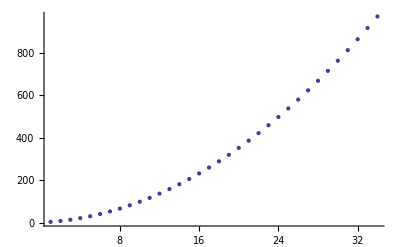

```mathematica
dataplot = ErrorBarPlots`ErrorListPlot[data]
```

```mathematica
fit=FindFit[Table[final[[i,1]],{i,1,Length[final]}],a x^2+b x+c,{a,b,c},x]
```

{a→0.783359,b→1.87181,c→2.08389}

```mathematica
F[x_]:=a x^2+b x+c
```

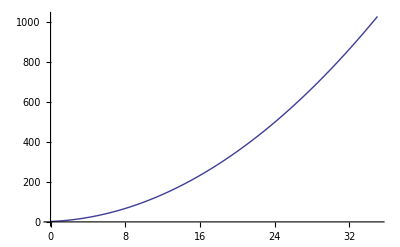

```mathematica
fitplot=Plot[F[x]/.fit,{x,0,35}]
```

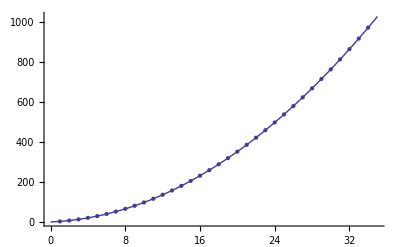

```mathematica
Show[dataplot,fitplot]
```